```mathematica
H[r_]:=1+L^(7-p)/r^(7-p);
A[r_]:=-1/4 Log[H[r]]
B[r_]:=1/4 Log[H[r]]
```

```mathematica
(p+1)Exp[-2 A[r]]Rμν+(9-p)Exp[-2 B[r]]Rmn//FullSimplify
```

-(L^14 (-7+p)^2 (-3+p) (1+p) r^(-2+2 p))/(4 √(1+L^(7-p) r^(-7+p)) (L^p r^7+L^7 r^p)^2)

```mathematica
Rμν=-Exp[2(A[r]-B[r])](A''[r]+(p+1)A'[r]^2+(7-p)A'[r]B'[r]+(8-p)/r A'[r])//FullSimplify
```

-(L^(14+p) (-7+p)^2 (-1+p) r^(5+2 p))/(8 (L^p r^7+L^7 r^p)^3)

```mathematica
H[r_]:=1+L^(7-p)/r^(7-p);
A[r_]:=-1/4 Log[H[r]]
B[r_]:=1/4 Log[H[r]]
Rμν=-Exp[2(A[r]-B[r])](A''[r]+(p+1)A'[r]^2+(7-p)A'[r]B'[r]+(8-p)/r A'[r])//FullSimplify;
Rmn=-(B''[r]+(p+1)A'[r] B'[r]+(7-p)( B'[r])^2+(2(7-p)+1)/r B'[r]+(p+1)/r A'[r])-1/(9-p)((7-p)B''[r]+(p+1)A''[r]-2 (p+1)A'[r] B'[r]+(p+1)(A'[r])^2-(7-p)(B'[r])^2-(7-p)/r B'[r]-(p+1)/r A'[r])//FullSimplify;
```

```mathematica
main=-(B''[r]+(p+1)A'[r] B'[r]+(7-p)( B'[r])^2+(2(7-p)+1)/r B'[r]+(p+1)/r A'[r]);
offdiag=-((7-p)B''[r]+(p+1)A''[r]-2 (p+1)A'[r] B'[r]+(p+1)(A'[r])^2-(7-p)(B'[r])^2-(7-p)/r B'[r]-(p+1)/r A'[r])//FullSimplify;
RicciSquared=(p+1)(Exp[-2 A[r]])^2 Rμν^2+(Exp[-2 B[r]])^2((9-p)main^2+2main*offdiag+offdiag^2)//FullSimplify
R=(p+1)Exp[-2 A[r]]Rμν+Exp[-2 B[r]]((9-p)main+offdiag)//FullSimplify
```

1/(32 (L^p r^7+L^7 r^p)^5)L^(14+p) (-7+p)^2 r^(3+2 p) (8 L^(2 p) (-9+p) (-8+p) (-3+p)^2 r^14+L^14 (1+p) (137+p (-1+(-9+p) p)) r^(2 p)-8 L^(7+p) (-8+p) (-5+p) (-3+p) (1+p) r^(7+p))

-(L^14 (-7+p)^2 (-3+p) (1+p) r^(-2+2 p))/(4 √(1+L^(7-p) r^(-7+p)) (L^p r^7+L^7 r^p)^2)

```mathematica
1/(32 (L^p r^7+L^7 r^p)^5)L^(14+p) (-7+p)^2 r^(3+2 p) (8 L^(2 p) (-9+p) (-8+p) (-3+p)^2 r^14+L^14 (1+p) (137+p (-1+(-9+p) p)) r^(2 p)-8 L^(7+p) (-8+p) (-5+p) (-3+p) (1+p) r^(7+p))/.p->3
```

(160 L^31 r^15)/((L^7 r^3+L^3 r^7)^5)

```mathematica
137+p (-1+(-9+p) p)//Expand
```

137-p-9 p^2+p^3

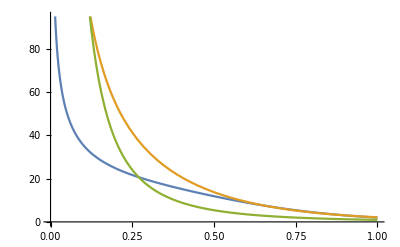

```mathematica
Plot[Table[1/(4 r^((p-3)/2))((p+1)(p-3)(p-7)^2)/((r^(7-p)+1)^(5/2)),{p,4,6}]//Evaluate,{r,0,1}]
```

```mathematica
Table[NSolve[r>0&&1/(4 r^((p-3)/2))((p+1)(p-3)(p-7)^2)/((r^(7-p)+1)^(5/2))==1,r],{p,4,6}]
```

{{{r→1.15892}},{{r→1.22213}},{{r→0.973141}}}

```mathematica
Solve[L^(2(7-p))/(4 r^((p-3)/2))((p+1)(p-3)(p-7)^2)/((L^(7-p))^(5/2))==1/l^2,r]//Simplify
```

{{r→16^(1/(3-p)) ((l^2 (-7+p)^2 (-3-2 p+p^2))/(√(L^(7-p))))^(2/(-3+p))}}

```mathematica
(*μ ν*)
μν=((p+1)p)/2(Exp[-2 B[r]] D[A[r],r]^2)^2//FullSimplify

(*μ i*)
(Exp[-2 B] D[A[r],r] D[B[r],r])^2;

xi^2/r^2 xj^2/r^2(Exp[-2B[r]] (D[A[r],{r,2}]+D[A[r],r]^2-2D[B[r],r] D[A[r],r]))^2;
(*sum over j*)
xi^2/r^2(Exp[-2B[r]] (D[A[r],{r,2}]+D[A[r],r]^2-2D[B[r],r] D[A[r],r]))^2;
(* Sum over i and mu*)
μi=
(9-p)(Exp[-2B[r]] (D[A[r],{r,2}]+(p-8)/r D[A[r],r]+D[A[r],r]^2-2D[B[r],r] D[A[r],r]))^2+(p+1)(9-p)(Exp[-2 B[r]] D[A[r],r] D[B[r],r])^2//FullSimplify

(*No cross term*)
(*ij*)
((9-p)(8-p))/2(Exp[-2 B[r]]D[B[r],r])^2;

xj^2/r^2 xk^2/r^2(D[B[r],{r,2}]+(p-8)/r D[A[r],r]-D[B[r],r] D[B[r],r])^2;
xj^2/r^2 xk^2/r^2(D[B[r],{r,2}]+(p-8)/r D[A[r],r]-D[B[r],r] D[B[r],r])^2;
(*sum over k, then over j and i*)
ij=((9-p)(8-p))/2(Exp[-2 B[r]] D[B[r],r]^2)^2+(9-p)(Exp[-2 B[r]](D[B[r],{r,2}]+(p-8)/r D[B[r],r]-D[B[r],r] D[B[r],r]))^2//FullSimplify
```

(L^(28+p) (-7+p)^4 p (1+p) r^(3+4 p))/(512 (L^p r^7+L^7 r^p)^5)

(L^(14+p) (-9+p) (-7+p)^2 r^(3+2 p) (-64 L^(2 p) (-8+p)^2 r^14-L^14 (274+p (5+(-12+p) p)) r^(2 p)-16 L^(7+p) (-15+p) (-8+p) r^(7+p)))/(256 (L^p r^7+L^7 r^p)^5)

(L^(14+p) (-9+p) (-7+p)^2 r^(3+2 p) (-128 L^(2 p) (-8+p)^2 r^14+L^14 (-2074+p (509+(-40+p) p)) r^(2 p)-32 L^(7+p) (-8+p) (-29+3 p) r^(7+p)))/(512 (L^p r^7+L^7 r^p)^5)

```mathematica
μν+μi+ij//FullSimplify
```

(L^(14+p) (-7+p)^2 r^(3+2 p) (-128 L^(2 p) (-9+p) (-8+p)^2 r^14-L^14 (-11799+p (3532+p (-339+10 p))) r^(2 p)-64 L^(7+p) (-11+p) (-9+p) (-8+p) r^(7+p)))/(256 (L^p r^7+L^7 r^p)^5)

```mathematica
D[B[r],r]
D[A[r],{r,2}]//FullSimplify
```

(L^(7-p) (-7+p) r^(-8+p))/(4 (1+L^(7-p) r^(-7+p)))

```mathematica
(L^7 (-7+p) r^(-2+p) (-L^p (-8+p) r^7))/(4 (L^p r^7)^2)//FullSimplify
```

-1/4 L^(7-p) (-8+p) (-7+p) r^(-9+p)

```mathematica
L^(14+p) (-7+p)^2 r^(3+2 p)  L^14 (24362+p (-9284+p (1291+(-70+p) p))) r^(2 p)/(256 (L^7 r^p)^5)//FullSimplify
```

1/256 L^(-7+p) (-7+p)^2 (24362+p (-9284+p (1291+(-70+p) p))) r^(3-p)

```mathematica
L^(14+p) (-7+p)^2 r^(3+2 p)16 L^(2 p) (-8+p)^2 (1+p) r^14/(256 (L^p r^7)^5)//FullSimplify
```

1/16 L^(14-2 p) (-8+p)^2 (-7+p)^2 (1+p) r^(2 (-9+p))

```mathematica
(L^28 (-9+p) (-7+p)^4 r^(-4+4 p) (-100 L^7 r^p))/(512 (L^p r^7)^5)
```

-25/128 L^(35-5 p) (-9+p) (-7+p)^4 r^(-39+5 p)

```mathematica
(L^14 (-9+p) (-7+p)^2 r^(-4+2 p) (4 L^(2 p) (-8+p) r^16))/(128 (L^p r^7)^4)
```

1/32 L^(14-2 p) (-9+p) (-8+p) (-7+p)^2 r^(-16+2 p)

```mathematica
1/(512 (L^p r^7+L^7 r^p)^6)L^14 (-7+p)^2 r^(-4+2 p) 16 L^(4 p) (-8+p) r^28 (-9+p) r^2
```

```mathematica
(L^(14+4 p) (-9+p) (-8+p) (-7+p)^2 r^(26+2 p))/(32 (L^p r^7)^6)//FullSimplify
```

1/32 L^(14-2 p) (-9+p) (-8+p) (-7+p)^2 r^(2 (-8+p))

```mathematica
1/(512 (L^p r^7+L^7 r^p)^6)L^14 (-7+p)^2 r^(-4+2 p) (-100 L^28 (-9+p) (-7+p)^2 r^(4 p))//FullSimplify
```

```mathematica
-(25 L^42 (-9+p) (-7+p)^4 r^(-4+6 p))/(128 (L^p r^6)^6)
```

-25/128 L^(42-6 p) (-9+p) (-7+p)^4 r^(-40+6 p)